# Revival Time Classic Vs Quantum

Authors: Alejandro Aguilar Salas, Carlos Manuel Rodríguez Martínez.

## Initialization cell

Source: http://mathematica.stackexchange.com/questions/16439/find-all-roots-of-an-interpolating-function-solution-to-a-differential-equation

```mathematica
Clear[findAllRoots]
SyntaxInformation[findAllRoots]={"LocalVariables"->{"Plot",{2,2}},"ArgumentsPattern"->{_,_,OptionsPattern[]}};
SetAttributes[findAllRoots,HoldAll];

Options[findAllRoots]=Join[{"ShowPlot"->False,PlotRange->All},FilterRules[Options[Plot],Except[PlotRange]]];

findAllRoots[fn_,{l_,lmin_,lmax_},opts:OptionsPattern[]]:=Module[{pl,p,x,localFunction,brackets},localFunction=ReleaseHold[Hold[fn]/.HoldPattern[l]:>x];
If[lmin≠lmax,pl=Plot[localFunction,{x,lmin,lmax},Evaluate@FilterRules[Join[{opts},Options[findAllRoots]],Options[Plot]]];
p=Cases[pl,Line[{x__}]:>x,Infinity];
If[OptionValue["ShowPlot"],Print[Show[pl,PlotLabel->"Finding roots for this function",ImageSize->200,BaseStyle->{FontSize->8}]]],p={}];
brackets=Map[First,Select[(*This Split trick pretends that two points on the curve are "equal" if the function values have _opposite _ sign.Pairs of such sign-changes form the brackets for the subsequent FindRoot*)Split[p,Sign[Last[#2]]==-Sign[Last[#1]]&],Length[#1]==2&],{2}];
x/.Apply[FindRoot[localFunction==0,{x,##1}]&,brackets,{1}]/.x->{}]
```

## Definitions

First of all its convenient to define some constant in order to simplify the calculations, L is the lenght of the square potential, M is the mass of the particle and k is related with 
its momentum and hence with his energy.

```mathematica
ℏ = 1; M = 1; L = 4;
ψcn[x_,k_]:=(2/L)^(1/2)Sin[(π x)/L] ⅇ^(ⅈ k x);
EF[n_,x_]:=(2/L)^(1/2)Sin[(n π x)/L];
En[n_]:=(π^2 ℏ^2)/(2M L^2)n^2;
```

## Wave Function of Time

In order to find the wave function at any time, we need to know the coefficients of the expansion in the energy eigenfunctions

```mathematica
c[n_,k_]=Integrate[ψcn[x,k]  EF[n,x],{x,0,L},Assumptions->{k ∈ Reals}];
ψt[x_,t_, k_]=Sum[c[n,k] EF[n,x] ⅇ^(-ⅈ/ℏ En[n]t), {n,1,100}];
```

If we wanna know what coefficients are the “heaviest” in the expansion in order to carry less terms in the expansion and make a efficient calculus, we plot the square absolute value of the constants c[n] (probabilities).

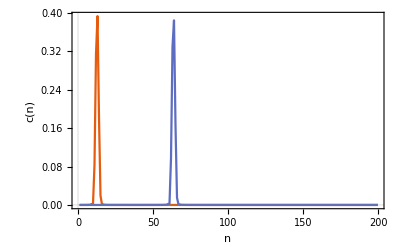

```mathematica
SetOptions[{ListPlot,ListLinePlot, Plot},BaseStyle->{FontSize->16}];
ListLinePlot[{Table[Abs[c[n,10]]^2,{n,1,200}],Table[Abs[c[n,50]]^2,{n,1,200}]},PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"n", "c(n)"},
Epilog->Inset[Column[{LineLegend[{Orange},{"k = 10"}],LineLegend[{Blue},{"k = 50"}]}],Scaled[{0.8,0.85}]]]
```

Another less visual way to know if the approximation is “good enough” is make the sum of the probabilities and see how close is to the unit, i.e:

```mathematica
Sum[N[Abs[c[n,2]]^2],{n,0,50}]
```

1.

## Time evolution

The probability distribution at any time is:

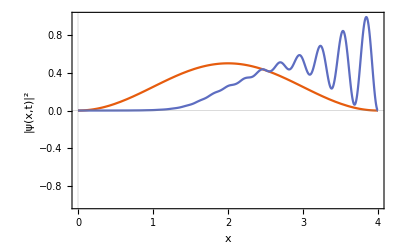

```mathematica
Plot[{Abs[ψt[x,0, 10]]^2,Abs[ψt[x,0.1, 10]]^2},{x,0,L},PlotRange->1,PlotTheme->"Scientific",FrameLabel->{"x", "|ψ(x,t)|^2"},Epilog->Inset[Column[{LineLegend[{Orange},{"t = 0"}],LineLegend[{Blue},{"t = 0.1"}]}],Scaled[{0.5,0.2}]]]
```

## Expected Value of the Position

Here we show the plot of the expected value of the position in function of t, and at least observationaly check that is a periodic value.

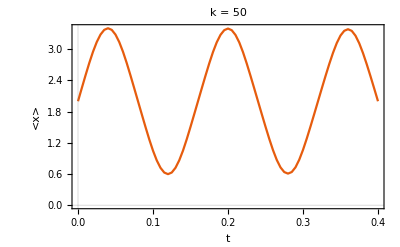

```mathematica
ex[t_, k_] := NIntegrate[x Abs[ψt[x,t,k]]^2,{x,0,L}];
ListLinePlot[ParallelTable[{t,ex[t,50]},{t,0,0.4,0.005}], PlotTheme->"Scientific",FrameLabel->{"t", "<x>"}, PlotLabel->"k = 50"]
```

## Contrast Quantum Vs Clasical

First classicaly we know exactly were the particle is in the square potential (position), and for that configuration, the time that take that particle to be in the same state (position and momentum) is given by:

T_RCl=L ((2M)/E)^(1/2)

As we say in the Definitions section, k its related with the particle’s momentum, so we can relate the clasical energy with the expected value of the energy and:

```mathematica
Sum[N[En[n] Abs[c[n]]^2],{n,1,200}]
```

2.30842

```mathematica
√((2 M)/Sum[N[En[n] Abs[c[n]]^2],{n,1,200}])L
```

3.72321

And the quantum revival time of the graph above is the same value.

## Quantum Revival time as a function of the energy.

Classical

Notice so far we have done all of those calculations for a specific value of the momentum and therefore for a specific energy, and for those values we find that the clasical revival time (or return time) its the same that the expected value of the position

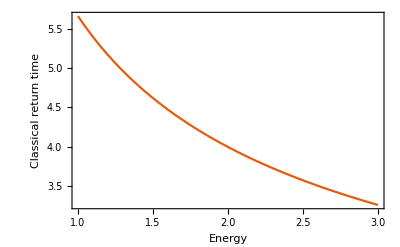

```mathematica
Subscript[t, RCl][En_]:=L ((2M)/En)^(1/2);
SetOptions[{ListPlot,ListLinePlot, Plot},BaseStyle->{FontSize->16}];
Plot[Subscript[t, RCl][En],{En,1,3},FrameLabel->{"Energy","Classical return time"},PlotTheme->"Scientific"]
```

Quantum, numeric, high energy

We can measure the Quantum return time by making a interpolation function from the expectation values of the position and measuring where is located the third value of 2 of the function.

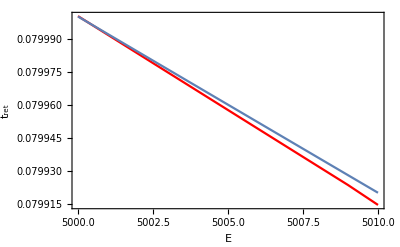

```mathematica
Clear[ψcn, EF, ψt,c, ex];
ℏ=1;M=1;L=4;
ψcn[x_,k_]:=(2/L)^(1/2) Sin[(π x)/L] E^(ⅈ k x);
EF[n_,x_]:=(2/L)^(1/2) Sin[(n π x)/L];
En[n_]:=(π^2 ℏ^2)/(2 M L^2) n^2;
c[n_,k_]=Integrate[ψcn[x,k] EF[n,x],{x,0,L},Assumptions->{k∈Reals}];
ψt[x_,k_,t_]=Sum[c[n,k] EF[n,x] E^(-(I/ℏ) En[n] t),{n,100,150}];

ex[t_,k_]:=NIntegrate[x Abs[ψt[x,k,t]]^2,{x,0,L}];
findReturnTime[Er_,range_]:=Module[{fu,roots,data},data=Table[{t,ex[t,Sqrt[(2 M Er)/ℏ^2]]},{t,0,range,range/10}];
data[[All,2]]=data[[All,2]]-2;
fu=Interpolation[data];
roots=findAllRoots[fu[t],{t,0,range}];
Return[{Er,roots[[3]]}]
];
returns=ParallelTable[findReturnTime[Er,0.2],{Er,5000,5010,1}];
tr[En_]:=L ((2M)/En)^(1/2);
SetOptions[{ListPlot,ListLinePlot, Plot},BaseStyle->{FontSize->16}];
Show[
{ListLinePlot[returns,PlotRange->Full, PlotStyle->Red, FrameLabel->{"E","t_ret"},PlotTheme->"Scientific"],
Plot[tr[En],{En,5000,5010},AxesLabel->{"Energy","Classical return time"}]},
Epilog->Inset[Column[{LineLegend[{Blue},{"Quantum"}],LineLegend[{Red},{"Classic"}]}],Scaled[{0.8,0.85}]]
]
```

Numeric, low energy

For lower energies the procedure is the same but we have to use lower values of the sum of ψt, and take the second value of 2 of the expectation value. This is because the interpolation function doesn’t have enough resolution to match the first value of 2.

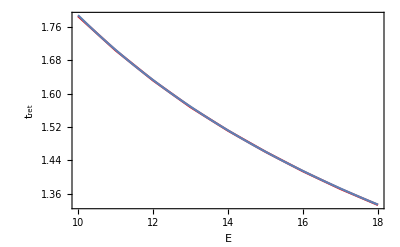

```mathematica
ℏ=1;M=1;L=4;
ψcn[x_,k_]:=(2/L)^(1/2) Sin[(π x)/L] E^(ⅈ k x);
EF[n_,x_]:=(2/L)^(1/2) Sin[(n π x)/L];
En[n_]:=(π^2 ℏ^2)/(2 M L^2) n^2;
c[n_,k_]=Integrate[ψcn[x,k] EF[n,x],{x,0,L},Assumptions->{k∈Reals}];
ψt[x_,k_,t_]=Sum[c[n,k] EF[n,x] E^(-(I/ℏ) En[n] t),{n,0,50}];

ex[t_,k_]:=NIntegrate[x Abs[ψt[x,k,t]]^2,{x,0,L}];
findReturnTime[Er_,range_]:=Module[{fu,roots,data},data=Table[{t,ex[t,Sqrt[(2 M Er)/ℏ^2]]},{t,0,range,range/10}];
data[[All,2]]=data[[All,2]]-2;
fu=Interpolation[data];
roots=findAllRoots[fu[t],{t,0,range}];
Return[{Er,roots[[2]]}]
];
returns=ParallelTable[findReturnTime[Er,2],{Er,10,18,1}];
tr[En_]:=L ((2M)/En)^(1/2);
SetOptions[{ListPlot,ListLinePlot, Plot},BaseStyle->{FontSize->16}];
Show[
{ListLinePlot[returns,PlotRange->Full, PlotStyle->Red, FrameLabel->{"E","t_ret"},PlotTheme->"Scientific"],
Plot[tr[En],{En,10,18},AxesLabel->{"Energy","Classical return time"}]},
Epilog->Inset[Column[{LineLegend[{Blue},{"Quantum"}],LineLegend[{Red},{"Classic"}]}],Scaled[{0.8,0.85}]]
]
```